# Practica 2 sesión 2

## Alumnos : David Laseca Pérez Zhuqing Wang

## EJERCICIO 1

### Implemente un módulo en Mathematica que, tomando como entrada un AFD proporcione como salida un AC unidireccional unidimensional que acepte el mismo lenguaje que el AFD mediante entrada paralela.

```mathematica
Ejercicio1[A_List]:=Module[{S,f,Sfinales,i,j},
(* Para obtener los estados del AC se unen los estados del AFD con su alfabeto*)
S=Union[A[[1]],A[[2]]];
(* Dado que para este tipo de AC la función es de la misma forma que las transiciones del AFD, la función de transición parte de estas transiciones *)
f=A[[3]];
(* Los estados finales coinciden con los del AFD, por lo que se obtienen directamente *)
Sfinales=A[[5]];
(* Para completar las transiciones de modo que ∀a,b∈Σ f(a,b)=b, se emplean unos bucles anidados que generan todas las primeras componentes de la transición para cada segundo componente *)
For[i=1,i≤Length[A[[2]]],i++,
For[j=1,j≤Length[A[[2]]],j++,
AppendTo[f,{A[[2,j]],A[[2,i]],A[[2,i]]}]
]
];
(* Se realiza el mismo proceso con los estados para que se cumpla ∀q,p∈Q f(q,p)=p *)
For[i=1,i≤Length[A[[1]]],i++,
For[j=1,j≤Length[A[[1]]],j++,
AppendTo[f,{A[[1,j]],A[[1,i]],A[[1,i]]}]
]
];
(* Se devuelve la composicion de los estados, la función de transición y los estados finales*)
Return[{S,f,Sfinales}]
]
```

```mathematica
AFDaux1={{q,p,r},{a,b},{{q,a,p},{q,b,r},{p,a,r},{p,b,q},{r,a,r},{r,b,r}},q,{r}}; (* Se define un AFD para comprobar el funcionamiento*)
```

```mathematica
Ejercicio1[AFDaux1] (*Se genera el AC con éxito *)
```

{{a,b,p,q,r},{{q,a,p},{q,b,r},{p,a,r},{p,b,q},{r,a,r},{r,b,r},{a,a,a},{b,a,a},{a,b,b},{b,b,b},{q,q,q},{p,q,q},{r,q,q},{q,p,p},{p,p,p},{r,p,p},{q,r,r},{p,r,r},{r,r,r}},{r}}

## EJERCICIO 2

### Implemente un módulo Mathematica que, tomando como entrada una cadena arbitraria, un AC que reconoce un lenguaje mediante entrada paralela en tiempo real y un estado de frontera q pertenece a S, proporcione como salida True si el AC acepta la cadena y False en caso contrario.

```mathematica
Ejercicio2[w_List,ac_List,q_]:=Module[{S,transition,Sf,dir,actual,der,next,i,j,posDer},
(* Se almacenan las componentes el AC en variables para trabajar más cómodamente *)
S=ac[[1]];
transition=ac[[2]];
Sf=ac[[3]];

(* Se comprueba si el AC es de tipo unidireccional o bidireccional *)
If[Length[transition[[1]]]==3,dir=True,dir=False];
(* Se incializa la célula actual *)
actual = q;
For[i=1,i≤Length[w],i++,
(* Se obtiene el valir de la célula de la derecha para el caso bidireccional *)
posDer=i+1;
If[posDer>Length[w],
der =q,
der=w[[posDer]]
];
(* Según si es bidireccional o no se calcula la transición de la manera correspondiente *)
If[dir,
next=Cases[transition,{actual,w[[i]],_}],
next=Cases[transition,{actual,w[[i]],der,_}]
];
(* Si no hubiese transición definida el AC rechazaría w *)
If[Length[next]==0,Return[False]];
(* Según si es bidireccional o no se calcula el siguiente valor de la célula *)
If[dir,
actual=next[[1,3]],
actual=next[[1,4]]
];
];
(* Finalmente se devuelve si el estado final de la célula de salida pertenece a los estados finales *)
Return[MemberQ[Sf,actual]]
];
```

```mathematica
ACaux1=Ejercicio1[AFDaux1];
```

```mathematica
ACaux2=Ejercicio3[AFDaux1];
```

```mathematica
Ejercicio2[{a,b,a,a,b},ACaux1,q]
```

True

```mathematica
Ejercicio2[{a,b,a,b,a},ACaux1,q]
```

False

```mathematica
Ejercicio2[{a,b,a,a,b},ACaux2,q]
```

True

```mathematica
Ejercicio2[{a,b,a,b,a},ACaux2,q]
```

False

## Ejercicio 3

### Proporcione una construcción formal para obtener a partir de un AFD, un AC equivalente unidimensional bidireccional (vecindario {-1, 0, 1}) con entrada paralela. Implemente un módulo en Mathematica que lleve a cabo la construcción propuesta.

```mathematica
Ejercicio3[A_List]:=Module[{S,f,Sfinales,i,j,k},
(* Para obtener los estados del AC se unen los estados del AFD con su alfabeto*)
S=Union[A[[1]],A[[2]]];
(* En este caso las transiciones del AFD no coinciden exactamente con la forma que deben tener en la función de transición del AC *)
f={};
(* Los estados finales coinciden con los del AFD, por lo que se obtienen directamente *)
Sfinales=A[[5]];
(* Para el caso del AC bidireccional se necesita un bucle anidado más que cubra todas las posibilidades de los estados de la célula de la derecha *)
For[i=1,i≤Length[A[[2]]],i++,
For[j=1,j≤Length[A[[2]]],j++,
(* Se incluye a la derecha el estado inicial, que será el de frontera *)
AppendTo[f,{A[[2,j]],A[[2,i]],A[[4]],A[[2,i]]}];
(* Y también se incluyen a la derecha los símbolos de las transiciones *)
For[k=1,k≤Length[A[[2]]],k++,
AppendTo[f,{A[[2,j]],A[[2,i]],A[[2,k]],A[[2,i]]}]
]
]
];
(* Se produce el mismo problema con los estados, y en este caso se deben añadir a la derecha tanto los estados como los símbolos de las transiciones *)
For[i=1,i≤Length[A[[1]]],i++,
For[j=1,j≤Length[A[[1]]],j++,
For[k=1,k≤Length[A[[2]]],k++,
AppendTo[f,{A[[1,j]],A[[1,i]],A[[2,k]],A[[1,i]]}]
];
For[k=1,k≤Length[A[[1]]],k++,
AppendTo[f,{A[[1,j]],A[[1,i]],A[[1,k]],A[[1,i]]}]
]
]
];
(* En último lugar se deben añadir las transiciones del AFD, para ello se les añaden a las transiciones los posibles estados de las celulas de la derecha, que son el estado de frontera y los símbolos de las transiciones del AFD *)
For[i=1,i≤Length[A[[3]]],i++,
AppendTo[f,{A[[3,i,1]],A[[3,i,2]],A[[4]],A[[3,i,3]]}];
For[j=1,j≤Length[A[[2]]],j++,
AppendTo[f,{A[[3,i,1]],A[[3,i,2]],A[[2,j]],A[[3,i,3]]}];
]
];
(* Finalmente se devuelven la composición de los estados, la función de transición y los estados finales *)
Return[{S,f,Sfinales}]
]
```

```mathematica
Ejercicio3[AFDaux1]
```

{{a,b,p,q,r},{{a,a,q,a},{a,a,a,a},{a,a,b,a},{b,a,q,a},{b,a,a,a},{b,a,b,a},{a,b,q,b},{a,b,a,b},{a,b,b,b},{b,b,q,b},{b,b,a,b},{b,b,b,b},{q,q,a,q},{q,q,b,q},{q,q,q,q},{q,q,p,q},{q,q,r,q},{p,q,a,q},{p,q,b,q},{p,q,q,q},{p,q,p,q},{p,q,r,q},{r,q,a,q},{r,q,b,q},{r,q,q,q},{r,q,p,q},{r,q,r,q},{q,p,a,p},{q,p,b,p},{q,p,q,p},{q,p,p,p},{q,p,r,p},{p,p,a,p},{p,p,b,p},{p,p,q,p},{p,p,p,p},{p,p,r,p},{r,p,a,p},{r,p,b,p},{r,p,q,p},{r,p,p,p},{r,p,r,p},{q,r,a,r},{q,r,b,r},{q,r,q,r},{q,r,p,r},{q,r,r,r},{p,r,a,r},{p,r,b,r},{p,r,q,r},{p,r,p,r},{p,r,r,r},{r,r,a,r},{r,r,b,r},{r,r,q,r},{r,r,p,r},{r,r,r,r},{q,a,q,p},{q,a,a,p},{q,a,b,p},{q,b,q,r},{q,b,a,r},{q,b,b,r},{p,a,q,r},{p,a,a,r},{p,a,b,r},{p,b,q,q},{p,b,a,q},{p,b,b,q},{r,a,q,r},{r,a,a,r},{r,a,b,r},{r,b,q,r},{r,b,a,r},{r,b,b,r}},{r}}

## Ejercicio 4

### Implemente un módulo Mathematica que muestre la secuencia de computación que se lleva a cabo en el módulo propuesto en la actividad (2) mediante un diagrama espaciotemporal. (Nota : Utilice las funciones ArrayPlot y ListAnimate explicados en la práctica de Fundamentos Básicos).

```mathematica
Ejercicio4[w_List,ac_List,q_]:=Module[{S,transition,Sf,dir,actual,der,resultado,inicial,aux,res,i,posDer,next},
(* Se almacenan las componentes el AC en variables para trabajar más cómodamente *)
S=ac[[1]];
transition=ac[[2]];
Sf=ac[[3]];
(* Se comprueba si el AC es de tipo unidireccional o bidireccional*)
If[Length[transition[[1]]]==3,dir=True,dir=False];
(* Se incializan las variables adecuadas *)
actual = q;
resultado={};
inicial={};
aux=w;
res={};
(* Se crea una configuración vacía *)
For[i = 1, i ≤ Length[w], i++,
AppendTo[inicial,0];
];
(* Se genera una serie de configuraciones de tamaño igual al que se tendrá al final del cálculo *)
For[i=1,i≤ Length[w],i++,
AppendTo[res,inicial];
];
(* Se le añade la configuración inicial y se calcula la primera gráfica *)
res=Insert[res,aux,1];
AppendTo[resultado,ArrayPlot[res,ColorRules->{S[[1]]->Red,S[[2]]->Blue,S[[3]]->Purple,S[[4]]->Yellow,S[[5]]->LightGreen}]];

For[i=1,i≤ Length[w],i++,
(* Se calcula la evolución de igual manera que en el ejercicio 2 *)
posDer=i+1;
If[posDer>Length[w],
der=q,
der=w[[posDer]]
];
If[dir,
next=Cases[transition,{actual,w[[i]],_}],
next=Cases[transition,{actual,w[[i]],der,_}]
];
(* En caso de rechazo se grafica la evolución hasta el instante actual *)
If[Length[next]==0,
Print[ListAnimate[resultado]];
Return[resultado]
];
If[dir,
actual=next[[1,3]],
actual=next[[1,4]];
];
(* Se modifican las variables que hayan cambiado en el periodo actual *)
aux=Delete[aux,i];
aux=Insert[aux,actual,i];
res=Delete[res,i+1];
res=Insert[res,aux,i+1];
(* Se añade la gráfica con la nueva configuración *)
AppendTo[resultado,ArrayPlot[res,ColorRules->{S[[1]]->Red,S[[2]]->Blue,S[[3]]->Purple,S[[4]]->Yellow,S[[5]]->LightGreen}]];
];
(* Finalmente se crea la animación con las gráficas y se devuelven para poder visualizarlas simultáneamente *)
Print[ListAnimate[resultado]];
Return[resultado]
];
```

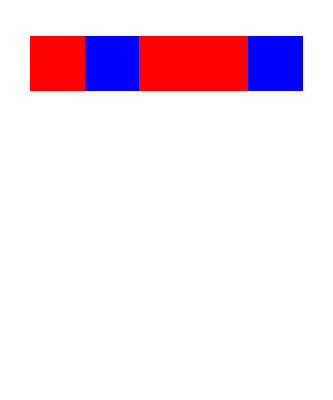
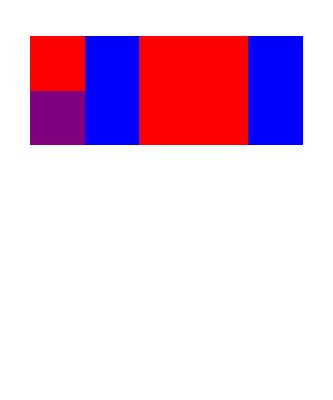
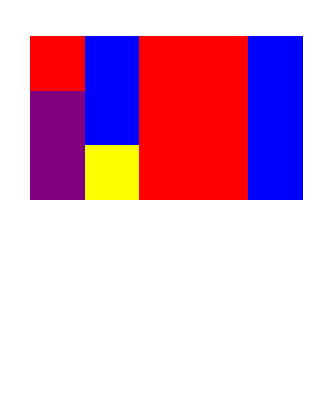
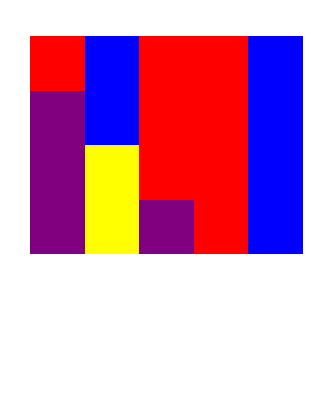
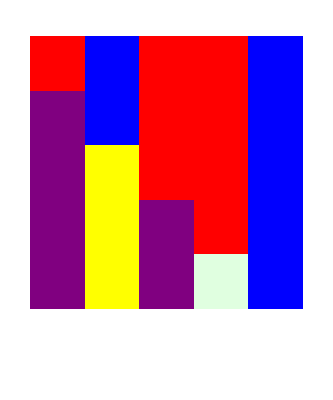
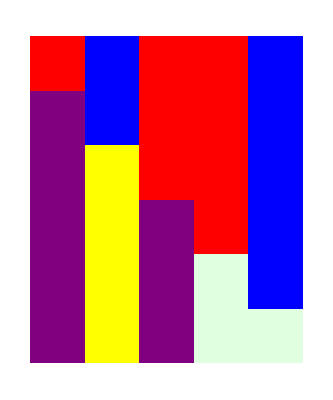

```mathematica
Ejercicio4[{a,b,a,a,b},ACaux1,q]
```

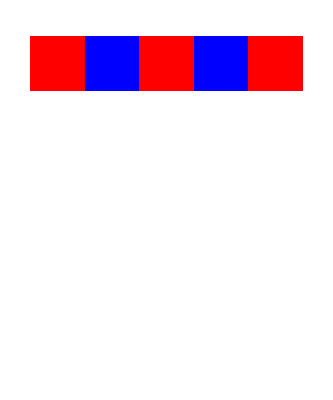
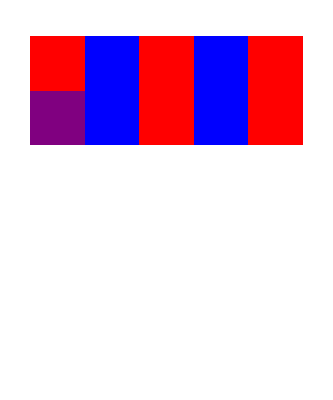
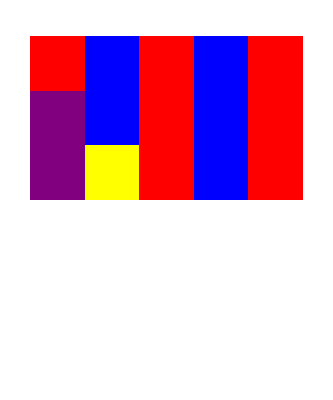
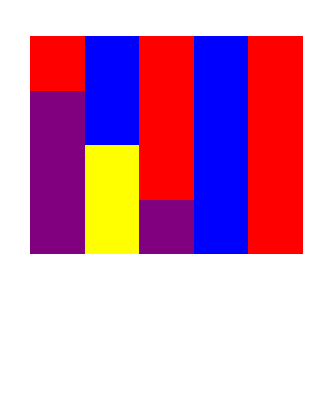
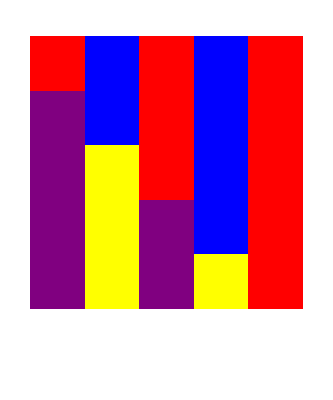
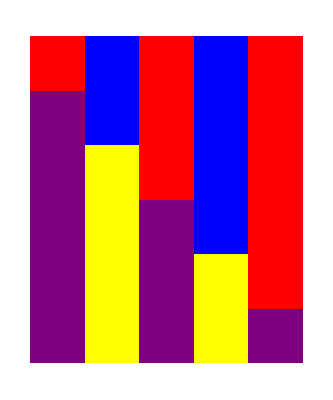

```mathematica
Ejercicio4[{a,b,a,b,a},ACaux1,q]
```